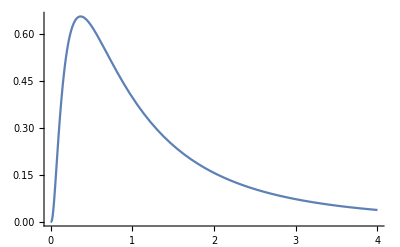

```mathematica
Plot[PDF[LogNormalDistribution[0,1],x],{x,0,4},PlotRange->All]
```

```mathematica
(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};
```

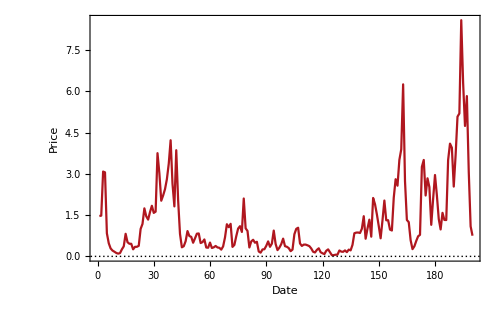

```mathematica
cQi = RandomVariate[LogNormalDistribution[0,0.5],200];
prices = FoldList[Times,cQi];
ListLinePlot[
prices,
PlotTheme->"Monochrome",
FrameLabel->{Style["Date",bigFontSize], Style["Price",bigFontSize]}, 

ImageSize->plotSize,
BaseStyle->FontSize->smallFontSize,
PlotMarkers->None,
PlotRangePadding->Automatic,
GridLines->{{},{0}},
PlotStyle->First[colors],
Frame->True,
PlotRange->All
]
```

```mathematica
prices = FoldList[Times,cQi];
```

```mathematica
Needs["EconomicComputations`"]
```

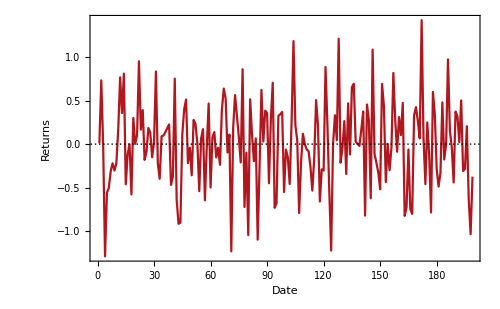

```mathematica
ListLinePlot[
Returns[prices],
PlotTheme->"Monochrome",
FrameLabel->{Style["Date",bigFontSize], Style["Returns",bigFontSize]}, 

ImageSize->plotSize,
BaseStyle->FontSize->smallFontSize,
PlotMarkers->None,
PlotRangePadding->Automatic,
GridLines->{{},{0}},
PlotStyle->First[colors],
Frame->True,
PlotRange->All
]
```

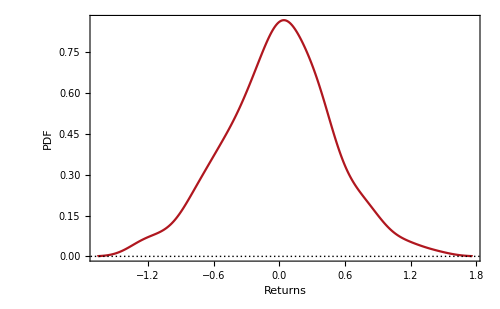

```mathematica
SmoothHistogram[
Returns[prices],
PlotTheme->"Monochrome",
FrameLabel->{Style["Returns",bigFontSize], Style["PDF",bigFontSize]}, 

ImageSize->plotSize,
BaseStyle->FontSize->smallFontSize,
PlotRangePadding->Automatic,
GridLines->{{},{0}},
PlotStyle->First[colors],
Frame->True,
PlotRange->All
]
```

```mathematica
FindDistribution[Returns[prices]]
```

NormalDistribution[-0.00213371,0.500322]